```mathematica
StringCases["this is a test string"," "~~x_ -> Framed[" "~~x]]
```

{ i, a, t, s}

```mathematica
StringReplace["Hello [username], this is me, [computer]","["~~Shortest[x___]~~"]"->"< the "~~ToUpperCase[x]~~" >"]
```

Hello < the USERNAME >, this is me, < the COMPUTER >

```mathematica
Select[Table[RomanNumeral[x],{x,1,100}],StringMatchQ[#,"X"~~x___~~"I"~~x___~~"V"]&]
```

{XIV}

```mathematica
StringCases["test 123 hello! 432",a:Whitespace~~x:DigitCharacter ..~~b:Whitespace:>a~~ToString[ToExpression[x]^2]~~b]
```

{ 15129 }

```mathematica
ToExpression["123"]
```

123

# Excercises

42.1

```mathematica
StringReplace["1 2 3 4",Whitespace->"---"]
```

1---2---3---4

```mathematica
TextCases[WikipediaData["computers"],DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter]//Sort
```

{1000,1235,1357,1357,1595,1613,1620,1630,1640,1770,1831,1833,1835,1872,1872,1876,1876,1888,1897,1901,1906,1920,1925,1927,1930,1934,1936,1936,1937,1938,1939,1940,1941,1942,1943,1943,1943,1943,1944,1945,1945,1945,1945,1945,1945,1947,1947,1947,1948,1948,1950,1950,1950,1950,1950,1951,1951,1952,1953,1953,1955,1955,1955,1957,1958,1958,1959,1959,1959,1962,1964,1967,1968,1970,1970,1970,1970,1990,2000,2000,2000,2000,2016,2400,2468,4000,4004,5000,5100,6502,6510}

```mathematica
Clear[x,headings];
headings = TextCases[WikipediaData["computers"],"==="~~Shortest[x__]~~"==="]
```

{=== Pre-20th century ===,=== First computing device ===,=== Analog computers ===,=== Digital computers ===,==== Electromechanical ===,==== Vacuum tubes and digital electronic circuits ===,=== Modern computers ===,==== Concept of modern computer ===,==== Stored programs ===,==== Transistors ===,==== Integrated circuits ===,=== Mobile computers ===,=== By architecture ===,=== By size, form-factor and purpose ===,=== History of computing hardware ===,=== Other hardware topics ===,=== Input devices ===,=== Output devices ===,=== Control unit ===,=== Central processing unit (CPU) ===,=== Arithmetic logic unit (ALU) ===,=== Memory ===,=== Input/output (I/O) ===,=== Multitasking ===,=== Multiprocessing ===,=== Languages ===,=== Programs ===,==== Stored program architecture ===,==== Machine code ===,==== Programming language ===,===== Low-level languages ===,===== High-level languages ===,==== Program design ===,==== Bugs ===,=== Computer architecture paradigms ===,=== Artificial intelligence ===}

```mathematica
Grid[Table[StringTemplate["<* #1 * #2 *>"][j,i],{j,1,9},{i,1,9}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81

```mathematica
Select[Table[IntegerName[j],{j,1,50}],StringMatchQ[#,___~~"i"~~___~~"e"~~___]&]
```

{five,nine,thirteen,fifteen,sixteen,eighteen,nineteen,twenty-five,twenty-nine,thirty-one,thirty-three,thirty-five,thirty-seven,thirty-eight,thirty-nine,forty-five,forty-nine}

```mathematica
StringReplace[First[TextSentences[WikipediaData["computers"]]],WordBoundary~~x:LetterCharacter~~y:LetterCharacter~~WordBoundary->ToUpperCase[x~~y]]
```

A computer IS a machine that can BE programmed TO carry out sequences OF arithmetic OR logical operations automatically.

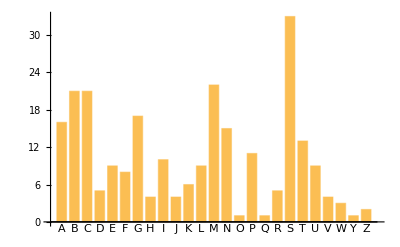

```mathematica
(Characters[#][[1]]&/@TextString/@EntityList["Country"])//Counts//BarChart[#,ChartLabels->Keys[#]]&
```

```mathematica
x = Counts[{1,2,1,1,2}];
```

<|1→3,2→2|>

```mathematica
Keys[x]
```

{1,2}

```mathematica
Clear[x]
```

```mathematica
Grid[Table[StringJoin[TextString[i],"^",TextString[j],"=",TextString[i^j]],{i,5},{j,5}]]
```

1^1=1 | 1^2=1 | 1^3=1 | 1^4=1 | 1^5=1
2^1=2 | 2^2=4 | 2^3=8 | 2^4=16 | 2^5=32
3^1=3 | 3^2=9 | 3^3=27 | 3^4=81 | 3^5=243
4^1=4 | 4^2=16 | 4^3=64 | 4^4=256 | 4^5=1024
5^1=5 | 5^2=25 | 5^3=125 | 5^4=625 | 5^5=3125

```mathematica
Grid[Table[StringTemplate["` `^` `=<*#1^#2*>"][i,j],{i,5},{j,5}]]
```

1^1=1 | 1^2=1 | 1^3=1 | 1^4=1 | 1^5=1
2^1=2 | 2^2=4 | 2^3=8 | 2^4=16 | 2^5=32
3^1=3 | 3^2=9 | 3^3=27 | 3^4=81 | 3^5=243
4^1=4 | 4^2=16 | 4^3=64 | 4^4=256 | 4^5=1024
5^1=5 | 5^2=25 | 5^3=125 | 5^4=625 | 5^5=3125